```mathematica
j[n_,x_]:=SphericalBesselJ[n,x]
h[n_,x_]:=SphericalBesselJ[n,x]+I SphericalBesselY[n,x]
```

```mathematica
b j[n,x]/x/(x D[h[n,x],x]- x h[n,x]D[j[n,x],x]/j[n,x]-b h[n,x])
```

(b SphericalBesselJ[n,x])/(x (-b (SphericalBesselJ[n,x]+ⅈ SphericalBesselY[n,x])-1/SphericalBesselJ[n,x]x (-SphericalBesselJ[n,x]/(2 x)+1/2 (SphericalBesselJ[-1+n,x]-SphericalBesselJ[1+n,x])) (SphericalBesselJ[n,x]+ⅈ SphericalBesselY[n,x])+x (-SphericalBesselJ[n,x]/(2 x)+1/2 (SphericalBesselJ[-1+n,x]-SphericalBesselJ[1+n,x])+ⅈ (-SphericalBesselY[n,x]/(2 x)+1/2 (SphericalBesselY[-1+n,x]-SphericalBesselY[1+n,x])))))

```mathematica
Sig[n_,x_,b_]:=(b SphericalBesselJ[n,x])/(x (-b (SphericalBesselJ[n,x]+ⅈ SphericalBesselY[n,x])-1/SphericalBesselJ[n,x] x (-SphericalBesselJ[n,x]/(2 x)+1/2 (SphericalBesselJ[-1+n,x]-SphericalBesselJ[1+n,x])) (SphericalBesselJ[n,x]+ⅈ SphericalBesselY[n,x])+x (-SphericalBesselJ[n,x]/(2 x)+1/2 (SphericalBesselJ[-1+n,x]-SphericalBesselJ[1+n,x])+ⅈ (-SphericalBesselY[n,x]/(2 x)+1/2 (SphericalBesselY[-1+n,x]-SphericalBesselY[1+n,x])))))
```

```mathematica
Crossesction[n_,x_,b_]:= (2 n +1)Abs[Sig[n,x,b]]^2
```

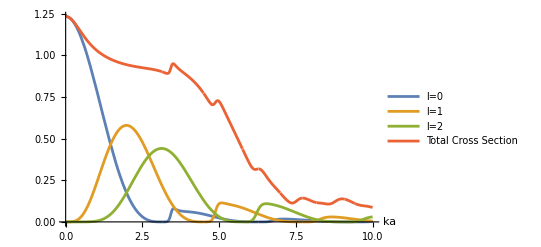

```mathematica
Plot[ {Crossesction[0,x,-10],Crossesction[1,x,-10],Crossesction[2,x,-10],Crossesction[0,x,-10]+Crossesction[1,x,-10]+Crossesction[2,x,-10]+Crossesction[3,x,-10]+Crossesction[4,x,-10]},{x,0,10},PlotLegends->{"l=0","l=1","l=2","Total Cross Section"},AxesLabel->{"ka",""}]
```

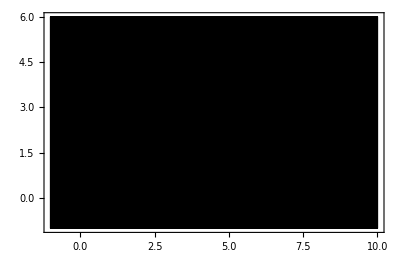

```mathematica
ComplexPlot[Sig[0,x,-10],{x,-1-1
I,10+6I},PlotLegends->Automatic]
```